```mathematica
Quit []
```

```mathematica
rOA = 0.5 * {Cos[θ], Sin[θ], 0.}
rOB = 0.4 * {0., 1., 0}
rAB = rOB - rOA
```

{0.5 Cos[θ],0.5 Sin[θ],0.}

{0.,0.4,0.}

{0.-0.5 Cos[θ],0.4-0.5 Sin[θ],0.}

```mathematica
nAB = Normalize[rAB]
```

{(0.-0.5 Cos[θ])/(√(0.+Abs[0.-0.5 Cos[θ]]^2+Abs[0.4-0.5 Sin[θ]]^2)),(0.4-0.5 Sin[θ])/(√(0.+Abs[0.-0.5 Cos[θ]]^2+Abs[0.4-0.5 Sin[θ]]^2)),0.}

```mathematica
mom = Cross[rOA, nAB]
```

{0.,0.,0.+(0.2 Cos[θ])/(√(Abs[0.-0.5 Cos[θ]]^2+Abs[0.4-0.5 Sin[θ]]^2))}

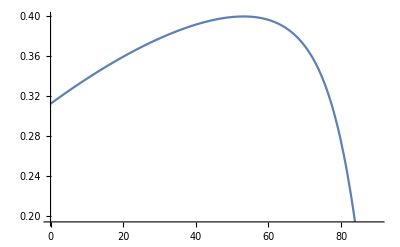

{0.4,{xθ→53.1301}}

```mathematica
mfun[θ_]:= (0.2 * Cos[θ]) / Sqrt[0.25 * Cos[θ]^2+(0.4-0.5 * Sin[θ])^2]
Plot[mfun[xθ Degree], {xθ, 0, 90.}]
FindMaximum[mfun[xθ Degree], {xθ, 0, 90.}] (*0, 90 are start, end*)
```